Helpers

```mathematica
Begin["READMETools`"];
$projimgs:=
FileBaseName/@
FileNames[
"*.png",
FileNameJoin@{ParentDirectory@NotebookDirectory[],"project","img"}
];
projimg[name_]:=FileNameJoin@{ParentDirectory@NotebookDirectory[],"project","img",name<>".png"};
backupimg[name_]:=
(
Quiet[CreateDirectory[FileNameJoin@{NotebookDirectory[],"backups","img"}]];
FileNameJoin@{NotebookDirectory[],"backups","img",
name<>"_"<>DateString["ISODateTime"]<>".png"}
);
projimgPad[img_?ImageQ]:=
ImagePad[
ImageCrop[
ImageResize[
ImagePad[
img,{{1,1},{0,0}},GrayLevel[.8]],
{Automatic,200}
],
{800,Full},
Padding->GrayLevel[.99]
],
1,
GrayLevel[.8]
];
projimgPad[name_String]:=
projimgPad@Import@projimg[name];
projimgExport[name_]:=
(
CopyFile[
projimg[name],
backupimg[name]
];
Export[
projimg[name],
projimgPad[name]
]
);
End[];
```

## ChemTools

ChemTools implements a suite of chemistry-oriented functionality, including a simple data framework, an object-oriented chemical modeling system, and a number of computational utilities on raw sets of atom and bonded systems

### Object-Oriented Chemistry

#### Packages

Objects

#### Description

Objects.m provides an object-oriented framework for chemical modeling and import. A rundown of the way it was built can be found here. The core data-types it provides are atoms, bonds, and atom sets. It integrates with a number of the other packages, such as Utilities and Psi4Connection to provide richer computational tools.

#### Examples

Import a molecule from PubChem:

```mathematica
ChemImport[methyloxirane]//ChemView
```

-Graphics3D-

Calculate the Gasteiger-charge based electric potential:

```mathematica
AtomsetElectricPotentialMap[methyloxirane]
```

-Graphics3D-

Plot the first molecular orbital:

```mathematica
AtomsetOrbitalsPlot[methyloxirane,
	"Orbitals"->1
	]
```

-Graphics3D-

### Data Framework

#### Packages

DataFramework

#### Description

DataFramework.m implements a simple, cached data-lookup system for a collection of different data types. It provides object-oriented access to data in a somewhat similar way to the built-in EntityFramework. Objects.m integrates with the data framework to provide atomic radii, standard bond distances, chemical structures, etc.

#### Examples

Lookup the SDF file for ethane:

```mathematica
ethaneSDF=ChemDataLookup["Ethane","SDFFiles"];
StringSplit[ethaneSDF,"M  END"->"M END"][[;;2]]//StringJoin
```

"6324
  -OEChem-09171715583D

  8  7  0     0  0  0  0  0  0999 V2000
   -0.7560    0.0000    0.0000 C   0  0  0  0  0  0  0  0  0  0  0  0
    0.7560    0.0000    0.0000 C   0  0  0  0  0  0  0  0  0  0  0  0
   -1.1404    0.6586    0.7845 H   0  0  0  0  0  0  0  0  0  0  0  0
   -1.1404    0.3501   -0.9626 H   0  0  0  0  0  0  0  0  0  0  0  0
   -1.1405   -1.0087    0.1781 H   0  0  0  0  0  0  0  0  0  0  0  0
    1.1404   -0.3501    0.9626 H   0  0  0  0  0  0  0  0  0  0  0  0
    1.1405    1.0087   -0.1781 H   0  0  0  0  0  0  0  0  0  0  0  0
    1.1404   -0.6586   -0.7845 H   0  0  0  0  0  0  0  0  0  0  0  0
  1  2  1  0  0  0  0
  1  3  1  0  0  0  0
  1  4  1  0  0  0  0
  1  5  1  0  0  0  0
  2  6  1  0  0  0  0
  2  7  1  0  0  0  0
  2  8  1  0  0  0  0
M END"

List the standard data sources:

```mathematica
$ChemDataSources//Keys
```

{AtomColors,BondDistances,UnitConversions,SpaceGroups,ElementValences,PubChemIDs,PubChemNames,ComponentIDs,ParentIDs,SimilarIDs,2DStructures,SDFFiles,PrimaryIsotope,StandardName,Symbol,Radius,Mass}

### Computational Utilities

#### Packages

Utilities

#### Description

Utilities.m provides a collection of simple utilities that operate largely on a collection of atoms and bonds. Objects.m makes extensive use of Utilities.m to provide methods of atomsets.

#### Examples

Compute the principal-axes system of the carbons in benzene:

```mathematica
carbons=Cases[AtomsetElementPositions@ChemImport[benzene],{"C",_}];
ChemUtilsInertialSystem[carbons]
```

<|A→7209.13,B→7208.63,C→3604.44,AAxis→{0.941414,-0.337253,-0.0000155897},BAxis→{-0.337253,-0.941414,0.0000181139},CAxis→{0.0000207853,0.000011795,1.},Units→1 MHz|>

Note that this is already included in Objects.m for atomset objects:

```mathematica
AtomsetInertialSystem[benzene]
```

<|A→5696.66,B→5696.28,C→2848.24,AAxis→{-0.948544,0.316646,0.0000135008},BAxis→{-0.316646,-0.948544,0.000011361},CAxis→{0.0000164035,6.50147×10^-6,1.},Units→1 MHz|>

Get the 1s hydrogen orbital:

```mathematica
ChemHOrbital[1,0][x,y,z]
```

0.081601096 ⅇ^(-0.944863063 x) x (10.-9.44863063 x+1.78553241 x^2) Cos[y]

Get the isotopologues of vinyl chloride with greater than 1% relative abundance:

```mathematica
atoms=AtomsetElementPositions@ChemImport["vinyl chloride"];
ChemUtilsIsotopologues[atoms,.01]
```

<|{{Chlorine35,{-1.4203,0.1932,0.}},{Carbon12,{0.158,-0.4694,0.}},{Carbon12,{1.2623,0.2762,0.}},{Hydrogen1,{0.1621,-1.5509,-0.0001}},{Hydrogen1,{2.2396,-0.1941,0.}},{Hydrogen1,{1.2208,1.36,0.}}}→0.741,{{Chlorine37,{-1.4203,0.1932,0.}},{Carbon12,{0.158,-0.4694,0.}},{Carbon12,{1.2623,0.2762,0.}},{Hydrogen1,{0.1621,-1.5509,-0.0001}},{Hydrogen1,{2.2396,-0.1941,0.}},{Hydrogen1,{1.2208,1.36,0.}}}→0.237|>

Note that these are all implemented in  top-level Mathematica code, and some may not operate well on large systems. For instance, computing symmetry elements gets prohibitively slow for larger systems:

```mathematica
ChemImport[water];
ChemUtilsSymmetryGraphics[AtomsetElementPositions@water]//AbsoluteTiming
```

```mathematica
ChemUtilsSymmetryGraphics[AtomsetElementPositions@benzene]//AbsoluteTiming
```

{1.28205,-Graphics3D-}

This can be accelerated by only considering the heavy atoms. The atom set version provides that as a default:

```mathematica
ChemView[benzene, "SymmetryElements"->All]//AbsoluteTiming
```

{0.436121,-Graphics3D-}

### External Connections

#### Packages

Extensions

SymbolicPython

Psi4Connection

SPConnection

OBConnection

#### Description

ChemTools provides a number of connections to programs written by others (running via ProcessObject as opposed to LibraryLink) although this may change in the future. To make this easier it supplies SymbolicPython.m for passing python code to, e.g. OpenBabel/PyBel or Psi4. Each connection provides a function for downloading and compiling. Generally these connections aren’t necessarily intended to be used oneself, but are built to make use of within higher-level systems.

#### Examples

Configure a simple scan in Psi4:

```mathematica
Needs["ChemTools`Psi4`"];
co=ChemImport["vinyl chloride"];
coels=AtomsetElementPositions@co;
com=ChemUtilsCenterOfMass@coels;
scanels=
	Append[
		ChemUtilsGenerateZMatrix@Append[coels,{"X",com}],
		{"Ar",Length[coels]+1,3.1077,2,180,1,#}
		];
scan=Psi4EnergyScan[
	<|
		"Molecules"->scanels,
		"Scan"->{{0,180,60}},
		"Configuration"->{
			"BasisSet"->"cc-pvqz"
			}
		|>
	]
```

Psi4Input[…]

Extract the input file string:

```mathematica
scan["input.dat"]//StringTrim
```

"molecule mol {
	Cl
	C 1 1.71174
	C 2 1.33244 1 123.2
	H 3 2.13278 2 24.9191 1 179.994
	H 4 2.48131 3 25.7972 2 179.994
	H 5 1.85827 4 89.9012 3 0.00139191
	X 6 2.13237 5 85.8944 4 0.00226565
	Ar 7 3.1077 2 180 1 pyVar_1
	}

set  { basis cc-pvqz }
for pyVar_1 in range(0, 180, 60):
	[ mol_1.pyVar_1 ] = [ pyVar_1 ]
	energy('scf')"

Find some of the properties of an OpenBabel molecule one can access:

```mathematica
Needs["ChemTools`OpenBabel`"]
importPyAsJSON=ImportString[StringReplace[#,{"'"->"\"","("->"[",")"->"]"}],"JSON"]&;
OBPyRun["C-C",
"pybelMol"."OBMol"//"dir"//Print
]//importPyAsJSON//RandomSample[#,10]&
```

{HasPartialChargesPerceived,UnsetLSSRPerceived,ConvertZeroBonds,HasSSSRPerceived,UnsetImplicitValencePerceived,DeleteBond,Kekulize,NewPerceiveKekuleBonds,Clear,GetBond}

Look at the pybel code generated to run this:

```mathematica
OBPyCommand["C-C",
"pybelMol"."OBMol"//"dir"//Print
]//StringTrim
```

"from __future__ import print_function
import openbabel, pybel
pybelLoadMolString = '''C-C'''
pybelLoadName = 'pybelMol'
pybelLoadFormat = 'SMILES'
pybelMol = pybel.readstring('SMILES', pybelLoadMolString)
pybelMol.inputString = pybelLoadMolString
pybelMol.inputFormat = pybelLoadFormat
pybelMol.inputName = pybelLoadName


print(dir(pybelMol.OBMol))"

Load a molecule in an interactive PyBel session:

```mathematica
OBPyRun[ChemDataLookup["vinyl chloride", "SDFFiles"]->"vcl",
	Print[ "vcl" ],
	"Session"->True
	]
```

ClC=C	6338

Find at the coordinates of the atoms of the vinyl chloride in the session:

```mathematica
OBPyRun[ChemDataLookup["vinyl chloride", "SDFFiles"]->"vcl",
	Print[ Map[#."coords"&, "vcl"."atoms" ]],
	"Session"->True
	]//importPyAsJSON
```

{{-1.4203,0.1932,0.},{0.158,-0.4694,0.},{1.2623,0.2762,0.},{0.1621,-1.5509,-0.0001},{2.2396,-0.1941,0.},{1.2208,1.36,0.}}

### Discrete Variable Representations

#### Packages

DVR

#### Description

DVR.m implements a framework for making and extending discrete variable representations, providing a basic object-oriented system for doing so. A few basic DVR classes have already been written which can be mixed and matched or used as it. Integration with Objects is forthcoming.

#### Examples

Load a simple 1D DVR and run it:

```mathematica
dvr=ChemDVRClass["Cartesian1DDVR"][{151}]
```

ChemDVRObject[…]

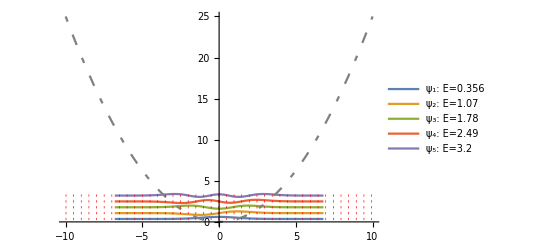

```mathematica
dvr[Manipulate->False]
```

### Spectroscopy

#### Packages

Spectroscopy

#### Description

Spectroscopy provides simple tools for working with spectra. It was designed for integrating with the spfit / spcat system that is popular with microwave spectroscopists.

#### Examples

Import a random JPL line list:

```mathematica
TemplateApply["https://spec.jpl.nasa.gov/ftp/pub/catalog/c``001.cat", IntegerString[RandomInteger[50],10,3]
]
```

```mathematica
spec=
	ChemSpectrumImport[
		TemplateApply["https://spec.jpl.nasa.gov/ftp/pub/catalog/c``001.cat",
			IntegerString[RandomInteger[50],10,3]
			]
		]
```

ChemSpectrum[…]

Plot it:

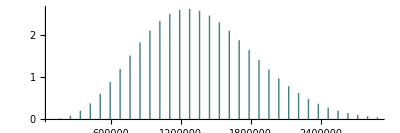

```mathematica
ChemSpectrumPlot[spec]
```

Start an interactive line picker

```mathematica
ChemSpectrumLineSelector[spec]
```

-Graphics-